```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
$PreRead=(#/. s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`50"&);

upper=Compile[{{method,_Real,0},{beta,_Real,0},{x,_Real,0},{n,_Real,0}},
Module[{k,xcp},
k=(2/(9n)) beta ;
xcp=(1-2 k)/(1+k);
If[n==0.,0,If[x>=n,n,If[x<=n xcp,n(1/(1+4 k)) (3 k+(1-2 k) x/n+3 Sqrt[k (k+x/n-(x/n)^2)]),n(((1-(4 beta)/(9 n))^2/(1+(2 beta)/(9 n))+√2 √((beta (-(1-(4 beta)/(9 n))^2/(1+(2 beta)/(9 n))^2+(1-(4 beta)/(9 n))/(1+(2 beta)/(9 n))+(2 beta)/(9 n)))/n)+(2 beta)/(3 n))/(1+(8 beta)/(9 n))+((1-(4 beta)/(9 n)+(beta (1-(2 (1-(4 beta)/(9 n)))/(1+(2 beta)/(9 n))))/(√2 √((beta (-(1-(4 beta)/(9 n))^2/(1+(2 beta)/(9 n))^2+(1-(4 beta)/(9 n))/(1+(2 beta)/(9 n))+(2 beta)/(9 n)))/n) n)) (-(1-(4 beta)/(9 n))/(1+(2 beta)/(9 n))+x/n))/(1+(8 beta)/(9 n)))]]]],RuntimeOptions->"Speed",CompilationTarget->"C"];
cf=Compile[{{s,_Real},{x,_Real},{mkni,_Real},{k1i,_Real},{n1i,_Real},{iter,_Integer}},
Module[{r,sum},
r=s;
sum=s;
Do[r=r (x-i) (mkni-i)/((k1i+i) (n1i+i));
sum+=r,{i,0,iter}];
sum],CompilationTarget->"C",RuntimeOptions->"Speed"];
```

```mathematica
hypepdf[m_,n_,k_,x_]:=Module[{mchosenln,xfactln,nminxfactln,fac},

If[m>=n>=x&&m>=k&&k>=x&&m>=k+n-x,
mchosenln=LogGamma[m+1]-LogGamma[n+1]-LogGamma[m-n+1];
xfactln=LogGamma[x+1];
nminxfactln=LogGamma[n-x+1];

fac=mchosenln+xfactln+nminxfactln;
Exp[(LogGamma[k+1]+LogGamma[m-k+1]-LogGamma[k-x+1]-LogGamma[m-k-n+x+1])-fac],

Print["Invalid Inputs"]]
]
```

```mathematica
hypecdf[m_,n_,k_,x_,s_,out_]:=Module[{c,mkni,k1i,n1i,xvar,iter,xvars,mknis,k1is,n1is,factors,sList},

If[m>=n>=x&&m>=k&&k>=x&&m>=k+n-x,

mkni=m-k-n+x;
k1i=k+1-x;
n1i=n+1-x;


iter=N[Min[4Sqrt[x],x],32];

xvar=x-iter;

xvars=Range[x,xvar,-1];
mknis=Range[mkni,mkni-iter,-1];
k1is=Range[k1i,k1i+iter];
n1is=Range[n1i,n1i+iter];



factors=xvars*mknis/(k1is*n1is);

sList=FoldList[Times,s,factors];


c=Total[sList];


If[out==1||xvar==0,c,c+Exp[-n ((xvar/n)Log[(xvar/n)/(k/m)]+(1-xvar/n)Log[(1-xvar/n)/(1-k/m)])]],

Print["Invalid Inputs"]]
]
```

```mathematica
upperBound[m_,n_,x_,p_]:=Module[{ratio,gam,norm,logp,chern,serf,low,high,prob,varlow,logprob,loghigh,iter,probhigh},


If[m>=n>=x,

ratio=x/n;
logp=Log[p];



gam=2 InverseErfc[2 p]^2(m-n)/(4 n (m-1));
norm= (1/(1+4gam))*(ratio+2gam+2*Sqrt[(gam(ratio(1-ratio)+gam))]);
chern=Round[upper[1,-logp,x,n]]/n;
serf=x/n+Sqrt[(m-n+1)(-logp)/(2m n)];


low=m ratio;
high=m  Min[1-(n-x+1)/m,chern,serf,norm];

probhigh=hypecdf[m,n,high,x,hypepdf[m,n,high,x],2];


If[probhigh>p,Print["epsilon is too low!!!"];probhigh,

loghigh=Log[probhigh];

varlow=Ceiling[low+(high-low)*(logp-Log[1/2])/(loghigh-Log[1/2])];
iter=0;

While[varlow<high&&iter<=5,
varlow=N[varlow,32];
prob=hypecdf[m,n,varlow,x,hypepdf[m,n,varlow,x],2];
If[prob<=p,Break[],logprob=Log[prob];varlow=Ceiling[varlow+(high-varlow)(logp-logprob)/(loghigh-logprob)]];

iter++

];


(*Print[prob];
varlow1=N[varlow,32]-1;
Print[hypecdf[m,n,varlow1,x,hypepdf[m,n,varlow1,x],1]];*)

Round[varlow]

],Print["Invalid Inputs"]]

];
```

```mathematica
hypepdfc=Compile[{{m,_Real,0},{n,_Real,0},{k,_Real,0},{x,_Real,0}},

Module[{mchosenln,xfactln,nminxfactln,fac},

mchosenln=LogGamma[m+1]-LogGamma[n+1]-LogGamma[m-n+1];
xfactln=LogGamma[x+1];
nminxfactln=LogGamma[n-x+1];

fac=mchosenln+xfactln+nminxfactln;

Exp[(LogGamma[k+1]+LogGamma[m-k+1]-LogGamma[k-x+1]-LogGamma[m-k-n+x+1])-fac]
]

,RuntimeOptions->"Speed",CompilationTarget->"C"];
```

```mathematica
hypecdfc=Compile[{{m,_Real,0},{n,_Real,0},{k,_Real,0},{x,_Real,0},{s,_Real,0},{out,_Integer,0}},Module[{c,mkni,k1i,n1i,xvar,iter,xvars,mknis,k1is,n1is,factors,sList},


mkni=m-k-n+x;
k1i=k+1-x;
n1i=n+1-x;

iter=Round[4 Sqrt[x]];

c=cf[s,x,mkni,k1i,n1i,iter];

xvar=x-iter;





If[out==1,c,c+Exp[-n ((xvar/n)Log[(xvar/n)/(k/m)]+(1-xvar/n)Log[(1-xvar/n)/(1-k/m)])]]]

,RuntimeOptions->"Speed",CompilationTarget->"C"
];
```

```mathematica
upperBoundc=Compile[{{m,_Real,0},{n,_Real,0},{x,_Real,0},{p,_Real,0}},Module[{ratio,gam,norm,logp,chern,serf,low,high,prob,varlow,logprob,loghigh,iter,log2},



ratio=x/n;
logp=Log[p];



gam=2 InverseErfc[2 p]^2(m-n)/(4 n (m-1));
norm= (1/(1+4gam))*(ratio+2gam+2*Sqrt[(gam(ratio(1-ratio)+gam))]);
chern=Round[upper[1,-logp,x,n]]/n;
serf=x/n+Sqrt[(m-n+1)(-logp)/(2m n)];


low=m ratio;
high=m  Min[1-(n-x)/m,chern,serf,norm];
loghigh=Log[hypecdfc[m,n,high,x,hypepdfc[m,n,high,x],2]];

log2=Log[1/2];
varlow=Ceiling[low+(high-low)*(logp-log2)/(loghigh-log2)];
iter=0;

While[varlow<high&&iter<=5,
prob=hypecdfc[m,n,varlow,x,hypepdfc[m,n,varlow,x],2];
logprob=Log[prob];
If[prob<=p,Break[],varlow=Ceiling[varlow+(high-varlow)(logp-logprob)/(loghigh-logprob)]];

iter++

];


Round[varlow]

]
,RuntimeOptions->"Speed",CompilationTarget->"C"
];
```

```mathematica
upperBoundmodc[m_,n_,x_,p_]:=Module[{ratio,gam,norm,logp,chern,serf,low,high,prob,varlow,logprob,loghigh,iter},



ratio=x/n;
logp=Log[p];



gam=2 InverseErfc[2 p]^2(m-n)/(4 n (m-1));
norm= (1/(1+4gam))*(ratio+2gam+2*Sqrt[(gam(ratio(1-ratio)+gam))]);
chern=Round[upper[1,-logp,x,n]]/n;
serf=x/n+Sqrt[(m-n+1)(-logp)/(2m n)];


low=m ratio;
high=m  Min[1-(n-x)/m,chern,serf,norm];
loghigh=Log[hypecdfc[m,n,high,x,hypepdf[m,n,high,x],2]];


varlow=Ceiling[low+(high-low)*(logp-Log[1/2])/(loghigh-Log[1/2])];
iter=0;

While[varlow<high&&iter<=5,
varlow=N[varlow,32];
prob=hypecdfc[m,n,varlow,x,hypepdf[m,n,varlow,x],2];
logprob=Log[prob];
If[prob<=p,Break[],varlow=Ceiling[varlow+(high-varlow)(logp-logprob)/(loghigh-logprob)]];

iter++

];


Round[varlow]

];
```

```mathematica
precision=32;
m=10^7;
n=RandomInteger[{1,Round[m/2]}]
x=RandomInteger[{1,Round[n/2]}]
m=N[m,precision];
n=N[n,precision] ;
x=N[x,precision];
p=N[10^-20,precision];
(*upperBoundc[m,n,x,p]//AbsoluteTiming

upperBoundmodc[m,n,x,p]//AbsoluteTiming*)

out=upperBound[m,n,x,p]//AbsoluteTiming

res=N[out[[2]],precision];

If[res>1,
{hypecdf[m,n,res,x,hypepdf[m,n,res,x],1],hypecdf[m,n,res-1,x,hypepdf[m,n,res-1,x],1]}]


(*pdf=hypepdf[m,n,N[out[[2]],precision],x];
pdfm=hypepdf[m,n,N[out[[2]],precision]-1,x];
m=N[m,$MachinePrecision];
n=N[n,$MachinePrecision];
x=N[x,$MachinePrecision];
res=N[out[[2]],$MachinePrecision];
{
hypecdf[m,n,res,x,hypepdf[m,n,res,x],1]//InputForm,hypecdf[m,n,res-1,x,hypepdf[m,n,res-1,x],1]//InputForm,
hypecdf[m,n,res,x,pdf,1]//InputForm,hypecdf[m,n,res-1,x,pdfm,1]//InputForm
}*)
```

714973

211061

{0.017137,3000324}

{9.9989195232590586375061×10^-21,1.0016839514435015725416×10^-20}

```mathematica
k=87;
iter=1;
Range[x,xvar,-1];
Range[m-k-n+x,mkni-iter,-1];
Range[k+1-x,k1i+iter];
Range[n+1-x,n1i+iter];
```

44.

7.

0.1590909090909090909090909090909

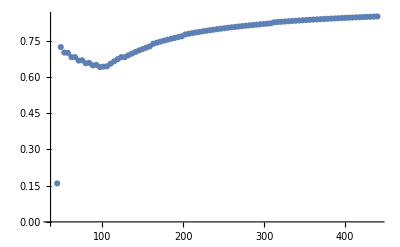

```mathematica
precision=32;
m=   10^2;
n=RandomInteger[{1,Round[m/2]}];
x=RandomInteger[{1,Round[n/2]}];
m=N[m,precision];
n=N[n,precision] ;
x=N[x,precision];
p=N[10^-20,precision];


n
x
frac=x/n

tab=ParallelTable[{i,Min[upperBoundmodc[i,n,x,p]/i]},{i,n ,10n,Max[n/10,1]}];
ListPlot[tab,ImageSize->Scaled[0.5],PlotRange->Full]
```

```mathematica
m=100;
k=upperBoundmodc[m,n,x,p]
hypepdfnew[m,n,k,x]
```

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

64

Error

Error

```mathematica
hypepdfnew[m_,n_,k_,x_]:=Module[{mchosenln,xfactln,nminxfactln,fac},
If[m>=n>=x&&m>=k&&k>=x&&m>=k+n-x,
mchosenln=LogGamma[m+1]-LogGamma[n+1]-LogGamma[m-n+1];
xfactln=LogGamma[x+1];
nminxfactln=LogGamma[n-x+1];

fac=mchosenln+xfactln+nminxfactln;
Exp[(LogGamma[k+1]+LogGamma[m-k+1]-LogGamma[k-x+1]-LogGamma[m-k-n+x+1])-fac]
,

Print["Error"]]
]
```

```mathematica
tab=Table[
precision=32;
m=10^9;
n=RandomInteger[{1,Round[m/2]}];
x=RandomInteger[{1,Round[n/2]}];
m=N[m,precision];
n=N[n,precision] ;
x=N[x,precision];
p=N[10^-20,precision];
{upperBoundc[m,n,x,p],upperBoundmodc[m,n,x,p],upperBound[m,n,x,p]},100];
AllTrue[tab,Equal@@#&]
```

True